# Annex to: “Non-formality of Voronov’s Swiss-Cheese operad”

## Najib Idrissi (Université Paris Cité and Sorbonne Université, CNRS, IMJ-PRG, F-75013 Paris, France) Renato Vasconcellos Vieira (Universidade de São Paulo, ICMC, São Carlos, Brasil)

See https://arxiv.org/abs/2303.16979 for the preprint of the main article.

```mathematica
SetDirectory[NotebookDirectory[]];
<<SwissCheeseCode`
```

## Helpers and structural operations

### Composition

```mathematica
exampleCubes=<|𝔠[1]->Cuboid[{0,-.8},{.9,-.2}],𝔠[2]->Cuboid[{.2,.3},{.4,1}]|>
```

<|𝔠[1]→Cuboid[{0,-0.8},{0.9,-0.2}],𝔠[2]→Cuboid[{0.2,0.3},{0.4,1}]|>

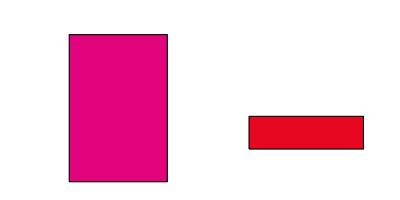

```mathematica
export["compos-outer.png",Framed[First[display2d[exampleCubes,Axes->False]],FrameStyle->LightGray]]
```

```mathematica
exampleCubes2=<|𝔠[1]->Cuboid[{0,-.8},{.2,.5}],𝔠[2]->Cuboid[{.4,-.3},{.7,1}]|>
```

<|𝔠[1]→Cuboid[{0,-0.8},{0.2,0.5}],𝔠[2]→Cuboid[{0.4,-0.3},{0.7,1}]|>

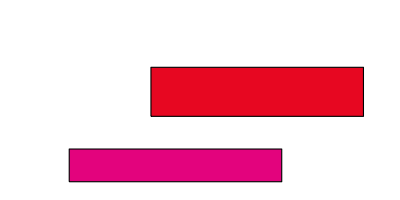

```mathematica
export["compos-inner.png",Framed[First[display2d[exampleCubes2,Axes->False]],FrameStyle->LightGray]]
```

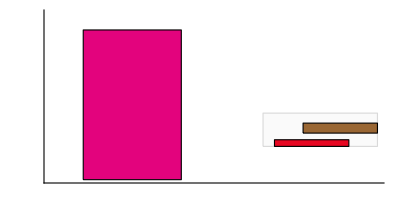

```mathematica
export["compos-result.png",Framed[First[display2d[γ[exampleCubes,Association[𝔠[2]->exampleCubes2]],Prolog->{EdgeForm[Directive[GrayLevel[0.85],Dashed]],GrayLevel[0.98],Reverse/@exampleCubes[𝔠[2]]}]],FrameStyle->LightGray]]
```

### Inclusion

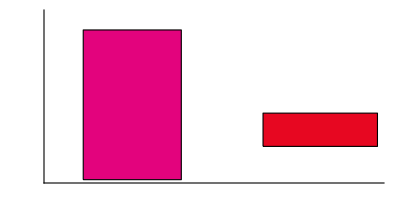

```mathematica
export["example-before.png",First@display2d[exampleCubes]]
```

```mathematica
export["example-inclusion-1.png",First@display[ι[{0},exampleCubes],PlotRange->{{0,1},{-1,1},{-1,1}}]]
```

-Graphics3D-

```mathematica
export["example-inclusion-2.png",First@display[ι[{1},exampleCubes]]]
```

-Graphics3D-

```mathematica
export["example-inclusion-3.png",First@display[ι[{2},exampleCubes]]]
```

-Graphics3D-

### The maps σ and τ

```mathematica
export["plot-sigma-tau.png",Plot[{σ[1,t],σ[-1,t],τ[{1},{t}],τ[{-1},{t}]+0.025},{t,-1,1},PlotLabels->TraditionalForm/@{SubPlus["σ"][t],SubMinus["σ"][t],SubPlus["τ"][t],SubPlus["τ"][t]},Frame->True]]
```

-Graphics-

```mathematica
export["plot-tau-3d.png",Plot3D[τ[{-1,-1},{s,t}],{s,-1,1},{t,-1,1},Exclusions->None]]
```

-Graphics3D-

## Non-formality in dimension 2

### Basic elements

```mathematica
format[μ[1]]
```

<|-→[0,1]×[-1,0],+→[0,1]×[0,1]|>

```mathematica
export["mu1.png",display2d[μ[1]]]
```

-Graphics-

```mathematica
format[α[1]]
```

<|𝔬→[0,1/2]×[-1,1],𝔠_1→[1/2,1]×[-1,1]|>

```mathematica
export["act1.png",display2d[α[1]]]
```

-Graphics-

### The loops

```mathematica
formatTable[Association[SubPlus["l"]^("1")->SubPlus[l][1][{t}],SubPlus["l"]^("2")->SubPlus[l][2][{Subscript[t, 1],Subscript[t, 2]}]]]
```

| 𝔠_1 | 𝔠_2
l_+^1 | [1/4 (1-2 Abs[t]),1/4 (3-2 Abs[t])]×[1/4 (-1-2 t),1/4 (1-2 t)] | [1/4 (-3+2 Abs[t]),1/4 (-1+2 Abs[t])]×[1/4 (-1+2 t),1/4 (1+2 t)]
l_+^2 | [1/4 (1-Max[2 Abs[t_1],2 Abs[t_2]]),1/4 (3-Max[2 Abs[t_1],2 Abs[t_2]])]×[1/4 (-1-2 t_1),1/4 (1-2 t_1)]×[1/4 (-1-2 t_2),1/4 (1-2 t_2)] | [1/4 (-3+Max[2 Abs[t_1],2 Abs[t_2]]),1/4 (-1+Max[2 Abs[t_1],2 Abs[t_2]])]×[1/4 (-1+2 t_1),1/4 (1+2 t_1)]×[1/4 (-1+2 t_2),1/4 (1+2 t_2)]

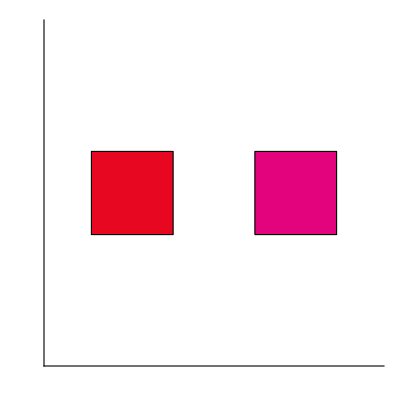
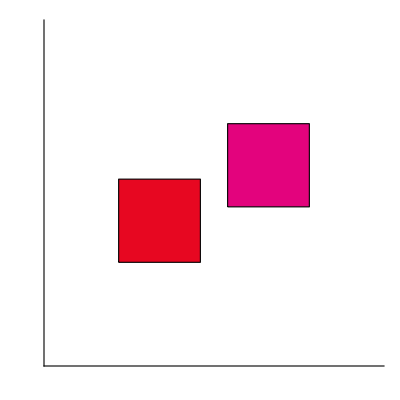
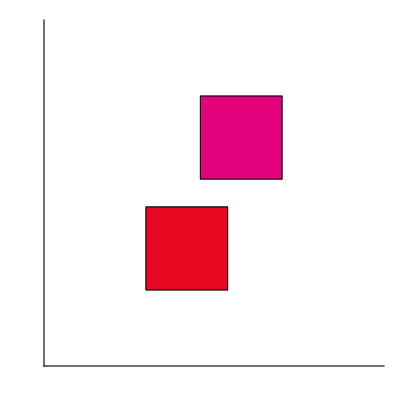
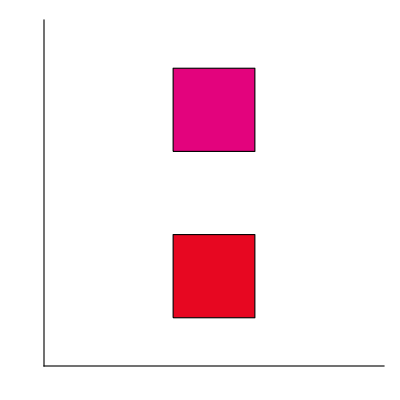
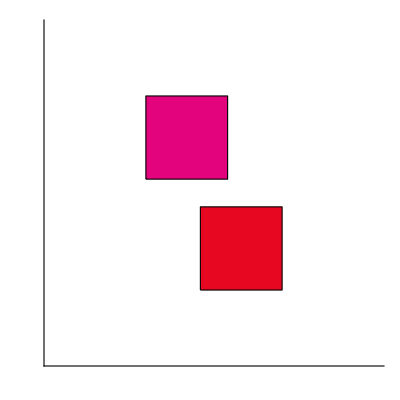
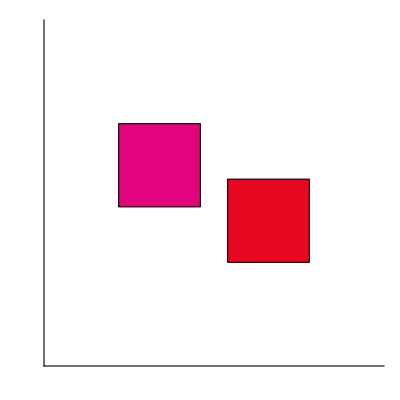
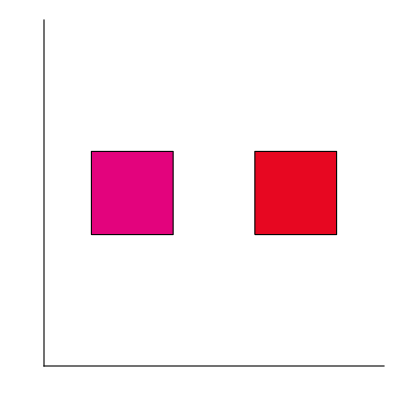
t==-1 | t==-2/3 | t==-1/3 | t==0 | t==1/3 | t==2/3 | t==1
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
export["l1plus.png",grid2d[SubPlus[l][1][{#}]&,3,PlotRange->{{-1,1},{-1,1}}]]
```

```mathematica
Manipulate[display2d[l[1][{t}],PlotRange->{{-1,1},{-1,1}}],{t,-1,1}]
```

The two halves of the loops do glue (example for n=2):

```mathematica
Reduce[∀_s∀_t(Abs[s]==1||Abs[t]==1)⇒SubPlus[l][2][{s,t}][𝔠[1]]==SubPlus[l][2][{-s,-t}][𝔠[2]]]
```

True

```mathematica
Manipulate[display[l[2][t],PlotRange->{{-1,1},{-1,1},{-1,1}}],{t,{-1,-1},{1,1}}]
```

### Non-formality of larger Swiss-Cheese

```mathematica
export["kappa.png",grid2d[κ,2]]
```

t==-1 | t==-1/2 | t==0 | t==1/2 | t==1
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

### Non-formality of Voronov’s Swiss Cheese

#### The chains β

```mathematica
formatTable[Association[Table[Subscript["β", 𝔬[ϵ]]->β[𝔬[ϵ]][{t}],{ϵ,{-1,1}}]]]
```

| 𝔠_1 | - | +
β_- | [1/2,1]×[-1,-Min[0,t]] | [0,1/2]×[-1,0] | [0,Max[1/2,(1+t)/2]]×[0,1]
β_+ | [1/2,1]×[Min[0,t],1] | [0,Max[1/2,(1+t)/2]]×[-1,0] | [0,1/2]×[0,1]

```mathematica
export["beta1plus.png",grid2d[β[𝔬[1]][{#}]&,1]]
```

t==-1 | t==0 | t==1
-Graphics- | -Graphics- | -Graphics-

```mathematica
export["beta1minus.png",grid2d[β[𝔬[-1]][{#}]&,1]]
```

t==-1 | t==0 | t==1
-Graphics- | -Graphics- | -Graphics-

```mathematica
Manipulate[display2d[β[𝔬[ϵ]][{t}]],{t,-1,1},{ϵ,{-1,1}}]
```

#### The chain η

```mathematica
Column[(format[#1][t]&)/@η1 plus components]
```

β_+∘_-α
  α∘_𝔬β_-
  α∘_𝔬β_+
  β_-∘_+α

```mathematica
formatTable[Association[SubPlus["η"]->SubPlus[η1][t]]]
```

| 𝔠_1 | 𝔠_2 | - | +
η_+ | [1/2,1]×[Piecewise[{{-1, t>-1/2}, {-3-4 t, -3/4<t≤-1/2}, {0, True}}],Piecewise[{{1, t≤1/2}, {3-4 t, 1/2<t<3/4}, {0, True}}]] | [Piecewise[{{1/4, -3/4≤t≤3/4}, {1/2 (-1-2 t), t<-3/4}, {1/2 (-1+2 t), True}}],Piecewise[{{1/2, -3/4≤t≤3/4}, {-1-2 t, t<-3/4}, {-1+2 t, True}}]]×[Piecewise[{{-1, t≤0}, {-1+4 t, 0<t<1/4}, {0, True}}],Piecewise[{{1, t>0}, {1+4 t, -1/4<t≤0}, {0, True}}]] | [0,Piecewise[{{1/4, -3/4≤t≤1/4}, {1/2, t>1/2}, {1/2 (-1-2 t), t<-3/4}, {t, True}}]]×[-1,0] | [0,Piecewise[{{1/4, -1/4≤t≤3/4}, {1/2, t≤-1/2}, {-t, -1/2<t<-1/4}, {1/2 (-1+2 t), True}}]]×[0,1]

```mathematica
export["eta1plus.png",grid2d[η1 plus,2]]
```

t==-1 | t==-1/2 | t==0 | t==1/2 | t==1
display2d[η1 plus[-1]] | display2d[η1 plus[-1/2]] | display2d[η1 plus[0]] | display2d[η1 plus[1/2]] | display2d[η1 plus[1]]

```mathematica
Manipulate[display2d[SubPlus[η1][t]],{t,-1,1}]
```

The chain η_+^1 glues to itself:

```mathematica
SubPlus[η1][1]==swapClosed[SubPlus[η1][-1]]
```

True

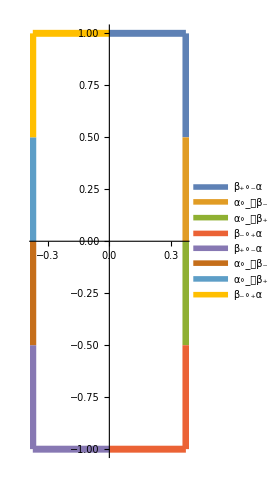

```mathematica
ParametricPlot[Evaluate[(Subtract@@RegionCentroid/@#1[s]⟦{Key[𝔠[1]],Key[𝔠[2]]}⟧&)/@η1 components],{s,-1,1},]
```

## Non-formality in dimension 3

```mathematica
export["mu-tot.png",display[μ[2]]]
```

-Graphics3D-

### The chains β^2

```mathematica
formatTable[Association[Table[Subscript["β", 𝔬[ϵ1,ϵ2]]^("2")->β[𝔬[ϵ1,ϵ2]][{s,t}],{ϵ1,{-1,1}},{ϵ2,{-1,1}}]]]
```

| 𝔠_1 | -- | -+ | +- | ++
β_(--)^2 | [1/2,1]×[-1,-Min[0,s]]×[-1,-Min[0,t]] | [0,1/2]×[-1,0]×[-1,0] | [0,Max[1/2,(1+t)/2]]×[-1,0]×[0,1] | [0,Max[1/2,(1+s)/2]]×[0,1]×[-1,0] | [0,Max[1/2,(1+s)/2,(1+t)/2]]×[0,1]×[0,1]
β_(-+)^2 | [1/2,1]×[-1,-Min[0,s]]×[Min[0,t],1] | [0,Max[1/2,(1+t)/2]]×[-1,0]×[-1,0] | [0,1/2]×[-1,0]×[0,1] | [0,Max[1/2,(1+s)/2,(1+t)/2]]×[0,1]×[-1,0] | [0,Max[1/2,(1+s)/2]]×[0,1]×[0,1]
β_(+-)^2 | [1/2,1]×[Min[0,s],1]×[-1,-Min[0,t]] | [0,Max[1/2,(1+s)/2]]×[-1,0]×[-1,0] | [0,Max[1/2,(1+s)/2,(1+t)/2]]×[-1,0]×[0,1] | [0,1/2]×[0,1]×[-1,0] | [0,Max[1/2,(1+t)/2]]×[0,1]×[0,1]
β_(++)^2 | [1/2,1]×[Min[0,s],1]×[Min[0,t],1] | [0,Max[1/2,(1+s)/2,(1+t)/2]]×[-1,0]×[-1,0] | [0,Max[1/2,(1+s)/2]]×[-1,0]×[0,1] | [0,Max[1/2,(1+t)/2]]×[0,1]×[-1,0] | [0,1/2]×[0,1]×[0,1]

```mathematica
export["theta-grid.png",grid[β[𝔬[1,1]][{##1}]&,2]]
```

| s==-1 | s==-1/2 | s==0 | s==1/2 | s==1
t==1 | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
t==1/2 | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
t==0 | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
t==-1/2 | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-
t==-1 | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D- | -Graphics3D-

```mathematica
Manipulate[display[β[𝔬[ϵ1,ϵ2]][st]],{st,{-1,-1},{1,1}},{ϵ1,{-1,1}},{ϵ2,{-1,1}}]
```

### The hemisphere

```mathematica
hemisphereLabels=(ReleaseHold[format[Hold[#1[_]]]]&)/@hemisphereComponents;
```

```mathematica
hemisphereCenters[s_,t_]=(Subtract@@RegionCentroid/@#1[{s,t}]⟦{Key[𝔠[1]],Key[𝔠[2]]}⟧&)/@hemisphereComponents;
```

```mathematica
ParametricPlot3D[Evaluate[hemisphereCenters[s,t]],{s,-1,1},{t,-1,1},PlotLegends->hemisphereLabels]
```

-Graphics3D-

## General case (n>=4)

There are no visualizations as the dimension is too large.

```mathematica
MatrixForm[Φ[{2,6},{3,5}][Array[Subscript[t, #1]&,6]]]
```

(Max[-Max[t_3,t_5],t_1]
Min[-Max[t_3,t_5],t_2]
Max[-Max[t_3,t_5],t_4]
Min[-Max[t_3,t_5],t_6])

```mathematica
MatrixForm[Ψ[Array[Subscript[t, #]&,6]]]
```

(t_1
t_2
t_3
t_4
Min[t_5,t_6])

```mathematica
μ[5,{3}]//format
```

<|-→[0,1]×[-1,1]×[-1,1]×[-1,0]×[-1,1]×[-1,1],+→[0,1]×[-1,1]×[-1,1]×[0,1]×[-1,1]×[-1,1]|>

```mathematica
μ[3,{1,2}]//format
```

<|--→[0,1]×[-1,0]×[-1,0]×[-1,1],-+→[0,1]×[-1,0]×[0,1]×[-1,1],+-→[0,1]×[0,1]×[-1,0]×[-1,1],++→[0,1]×[0,1]×[0,1]×[-1,1]|>

```mathematica
α[3]//format
```

<|𝔬→[0,1/2]×[-1,1]×[-1,1]×[-1,1],𝔠_1→[1/2,1]×[-1,1]×[-1,1]×[-1,1]|>

```mathematica
β[6,{2,5},𝔬[-1,1]][{Subscript[t, 2],Subscript[t, 5]}]//format
```

<|--→[0,Max[1/2,1/2 (1+t_5)]]×[-1,1]×[-1,0]×[-1,1]×[-1,1]×[-1,0]×[-1,1],-+→[0,1/2]×[-1,1]×[-1,0]×[-1,1]×[-1,1]×[0,1]×[-1,1],+-→[0,Max[1/2,1/2 (1+t_2),1/2 (1+t_5)]]×[-1,1]×[0,1]×[-1,1]×[-1,1]×[-1,0]×[-1,1],++→[0,Max[1/2,1/2 (1+t_2)]]×[-1,1]×[0,1]×[-1,1]×[-1,1]×[0,1]×[-1,1],𝔠_1→[1/2,1]×[-1,1]×[-1,-Min[0,t_2]]×[-1,1]×[-1,1]×[Min[0,t_5],1]×[-1,1]|>